# Transform2DPlot Gallery

```mathematica
Get[StringJoin[NotebookDirectory[],"Transform2DPlot.wl"]]
```

## Graphic Gallery 1

#### {Sin[x] y,x+Cos[y]}

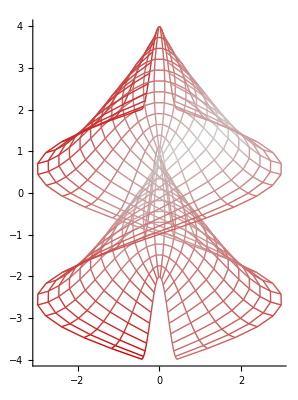

```mathematica
Transform2DPlot[{Sin[x] y,x+Cos[y]},{x,-3,3},{y,-3,3},PlotRange->All]
```

#### Sin[x y] {x, y}

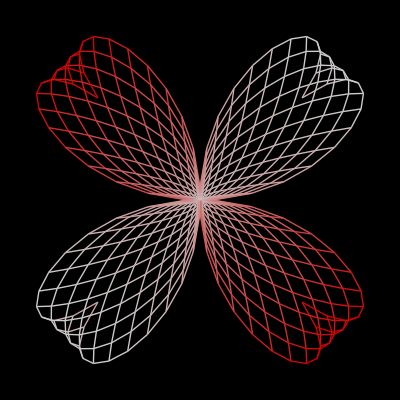

```mathematica
Transform2DPlot[Sin[x y] {x,y},{x,-π/2,π/2},{y,-π/2,π/2},Background->GrayLevel[0],Axes->False]
```

#### on rectangular grid, moth

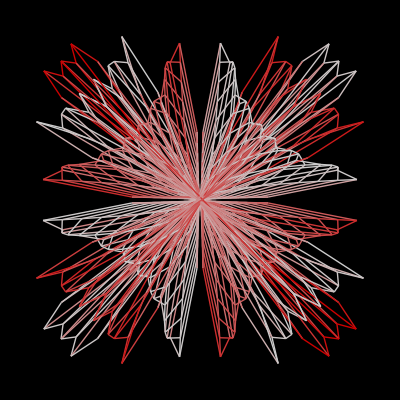

```mathematica
Transform2DPlot[Sin[x y] {x,y},{x,-π,π},{y,-π,π},Background->GrayLevel[0],Axes->False]
```

#### explosion

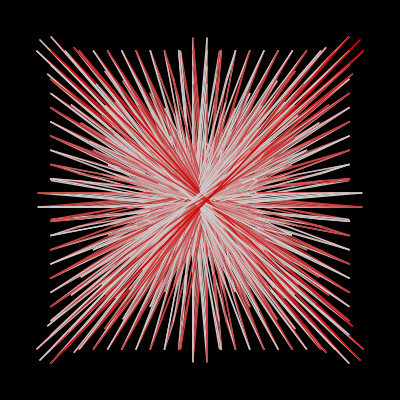

```mathematica
Transform2DPlot[Sin[x y] {x,y},{x,-2 π,2 π},{y,-2 π,2 π},Background->GrayLevel[0],Axes->False]
```

#### on concentric circles

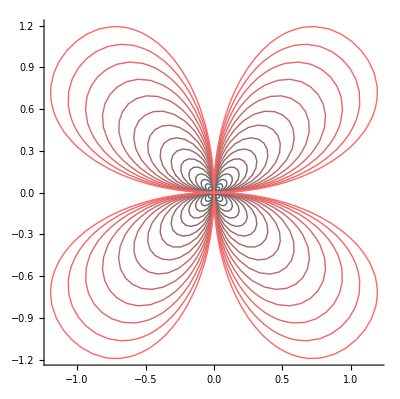

```mathematica
Transform2DGraphicsPlot[Table[{RGBColor[i/(π/2),0.4,0.4],Circle[{0,0},i]},{i,0,π/2,π/(2 20)}],Function[{x,y},Sin[x y] {x,y}],ResolutionLength->.1,AspectRatio->Automatic,Axes->True]
```

#### on a triangular grid, butterfly

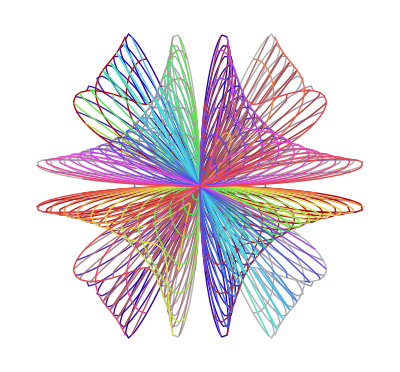

```mathematica
Transform2DGraphicsPlot[TriangularGrid[π,30,{Hue[.7,#1,.7]&,Hue[0,#1,.7]&,Hue[#1,.7,.9]&}],Function[{x,y},Sin[x y] {x,y}],AspectRatio->Automatic]
```

#### amethyst

Animation of the function applied to a increasingly larger rectangular grid.

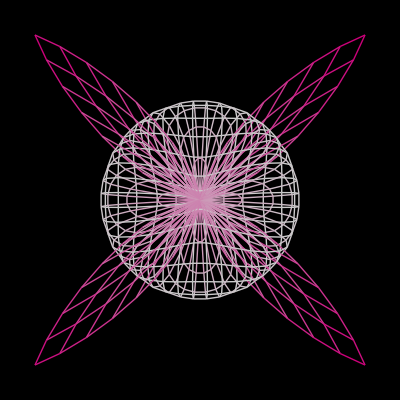
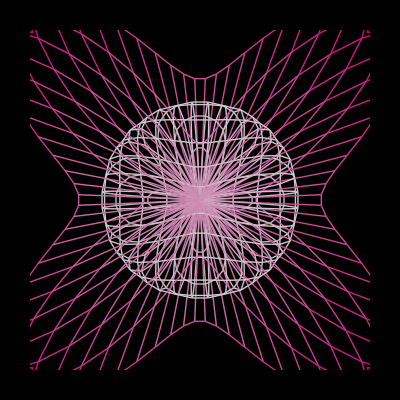
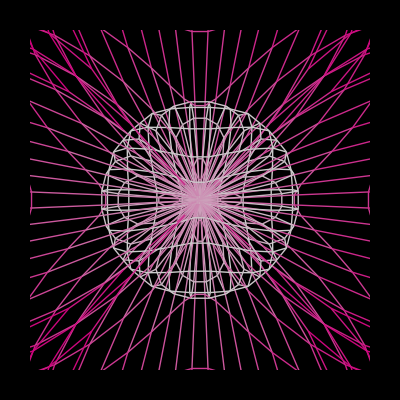
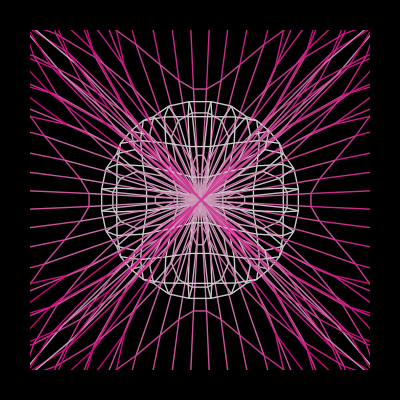
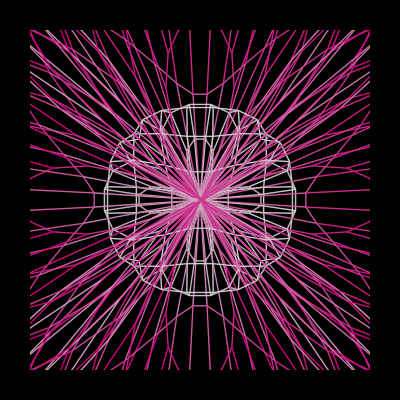
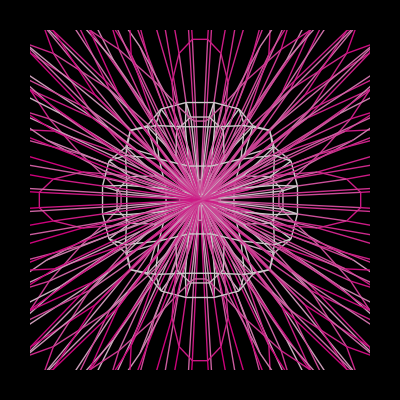

```mathematica
Table[Transform2DPlot[Sin[Norm[{#1,#2}]] {#1,#2}&,{-1,1} i,{-1,1} i,ColorFunction->(Hue[.9,#1,.8]&),Background->GrayLevel[0],Axes->False,PlotRange->{{-1,1},{-1,1}} 3],{i,π,2 π,π/5}]
```

Animation of the function Sin[Norm[{#1,#2}]] {#1,#2}&
applied to a increasing larger triangular grid.

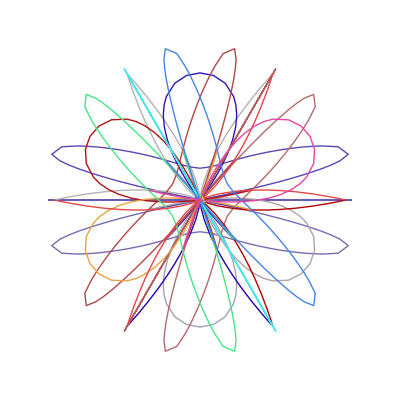
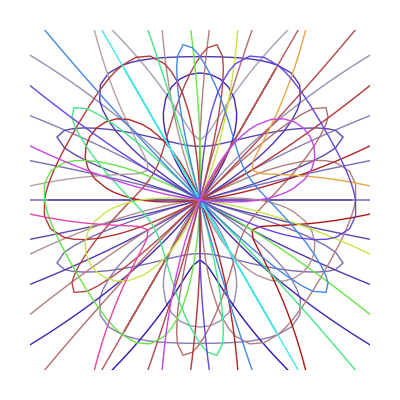
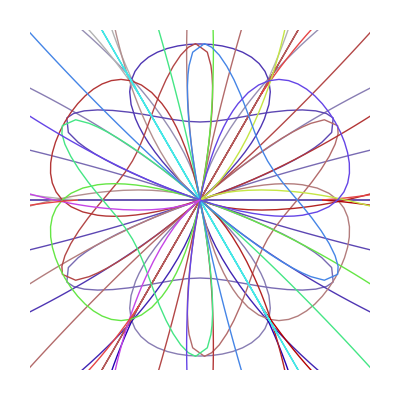
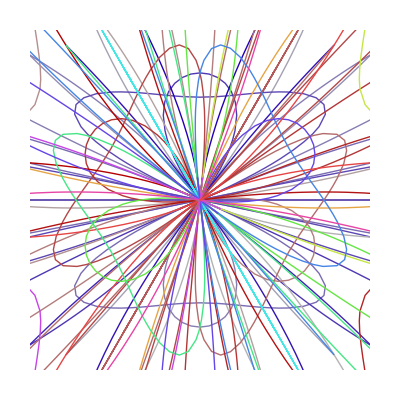

```mathematica
Table[Transform2DGraphicsPlot[TriangularGrid[i, 11, 
    {Hue[0.7, #1, 0.7] & , Hue[0, #1, 0.7] & , Hue[#1, 0.7, 0.9] & }], 
   Sin[Norm[{#1, #2}]]*{#1, #2} & , ResolutionLength -> 0.2, 
   AspectRatio -> Automatic, PlotRange -> {{-1, 1}, {-1, 1}}*1.9], 
  {i, Pi, 2*Pi, Pi/3}]
```

#### On polar grid. Stars Streak

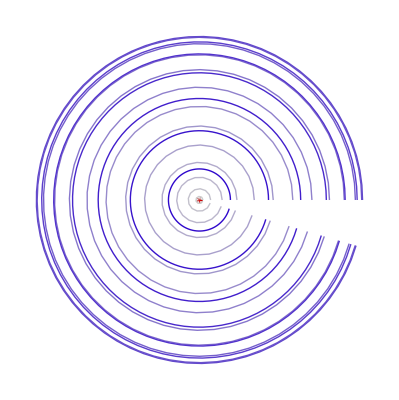

```mathematica
Transform2DGraphicsPlot[PolarGrid[{0.2,π,π/20},{0,6,6/5}],Sin[Norm[{#1,#2}]] {#1,#2}&,ResolutionLength->0.2,AspectRatio->Automatic]
```

#### electric fan

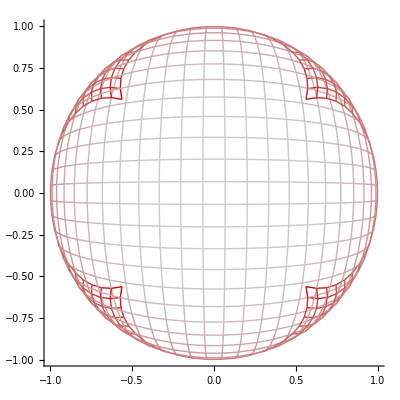
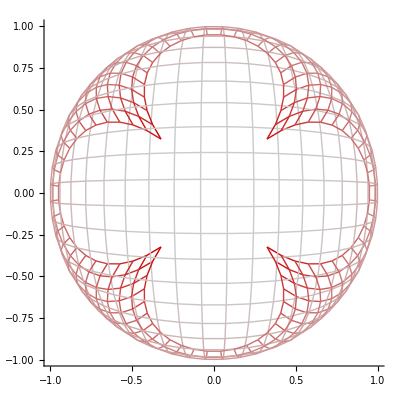
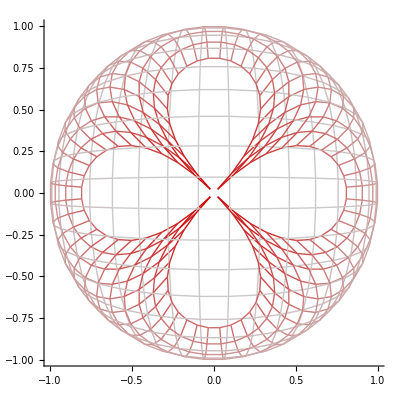
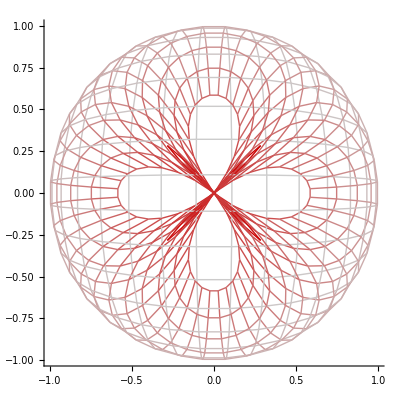
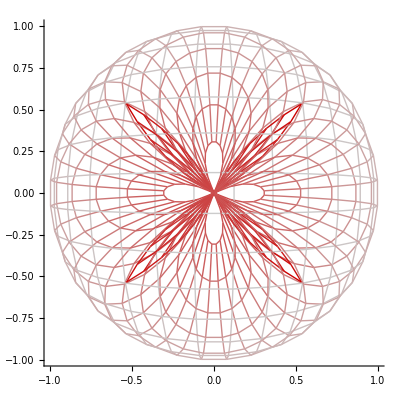
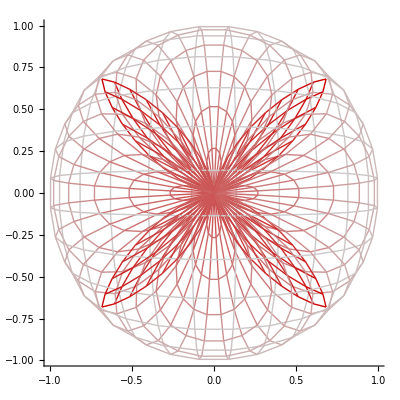

```mathematica
Table[Transform2DPlot[Sin[Norm[{x,y}]] Normalize[{x,y}],{x,-i,i},{y,-i,i},Axes->True],{i,π/2,π,π/(2 5)}]
```

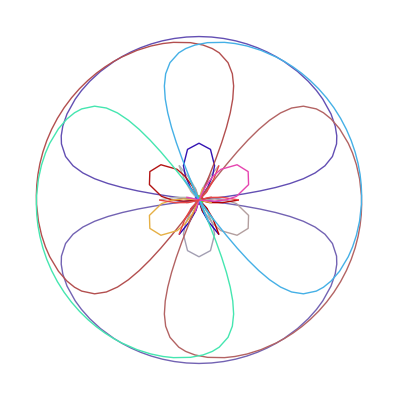
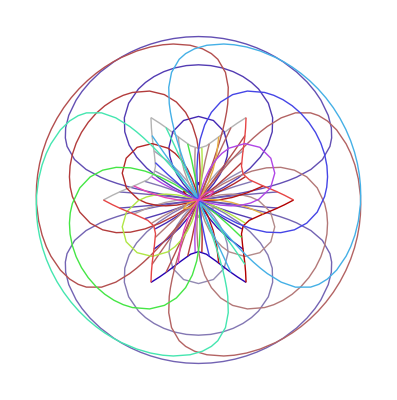
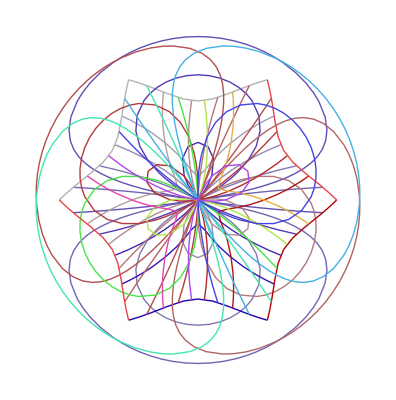
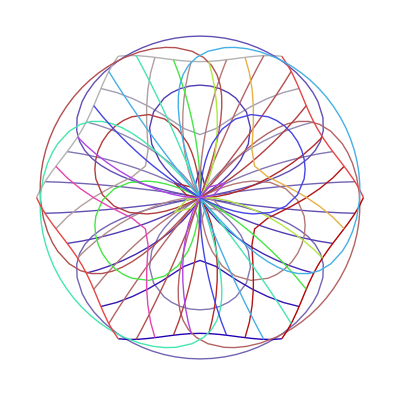
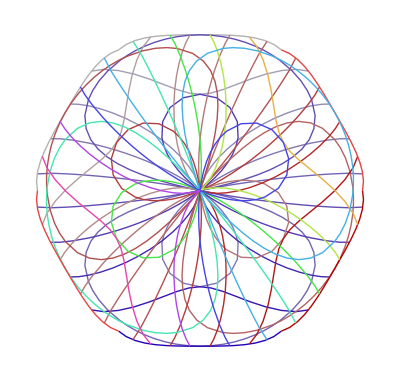
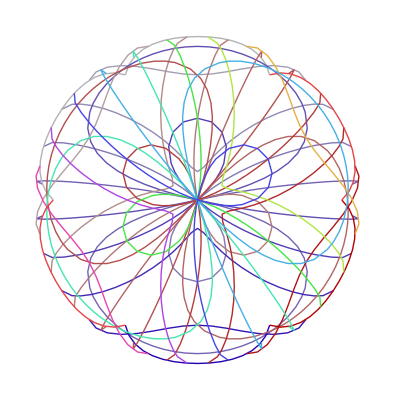

```mathematica
Table[Transform2DGraphicsPlot[TriangularGrid[i,10,{Hue[0.7,#1,0.7]&,Hue[0,#1,0.7]&,Hue[#1,0.7,0.9]&}],Function[{x,y},Cos[Norm[{x,y}]] Normalize[{x,y}]],ResolutionLength->π/30,AspectRatio->Automatic],{i,π/2,π,π/(2 5)}]
```

#### waves

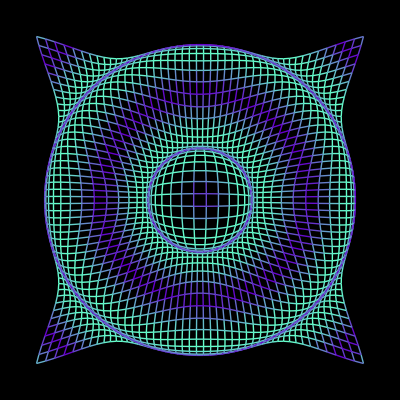

```mathematica
Transform2DPlot[Sin[Norm[{x, y}]]*Normalize[{x, y}] + {x, y}, 
  {x, -3*Pi, 3*Pi}, {y, -3*Pi, 3*Pi}, PlotPoints -> {1, 1}*50, 
  ColorFunction -> (RGBColor[0.4, #1, 0.8] & ), Background -> GrayLevel[0], 
  Axes -> False]
```

#### wave 2

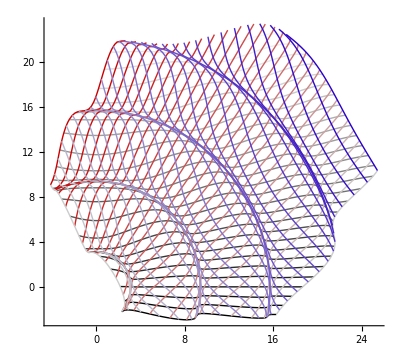

```mathematica
Transform2DGraphicsPlot[TriangularGrid[4 π,30,{10,10}],Function[{x,y},Sin[Norm[{x,y}]] Normalize[{x,y}]+{x,y}],ResolutionLength->.5,AspectRatio->Automatic,Axes->True]
```

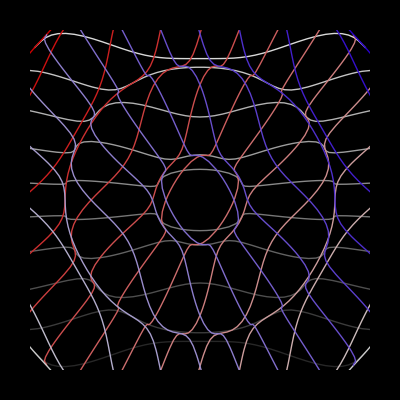
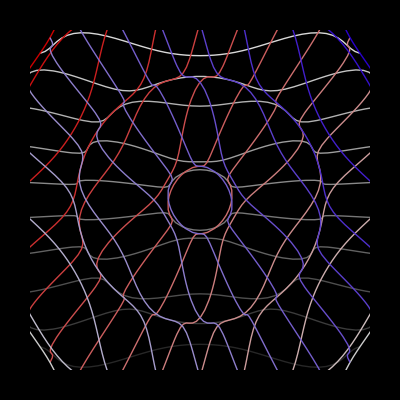
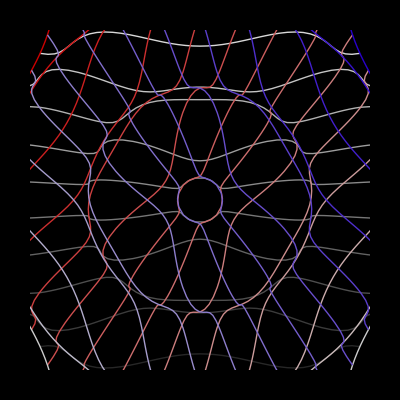
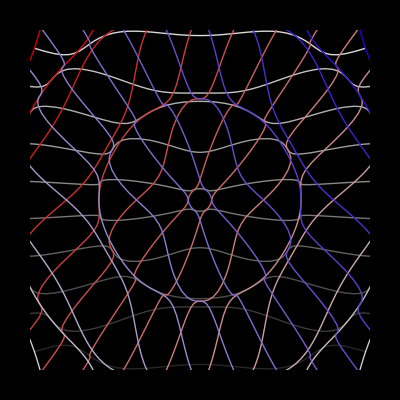
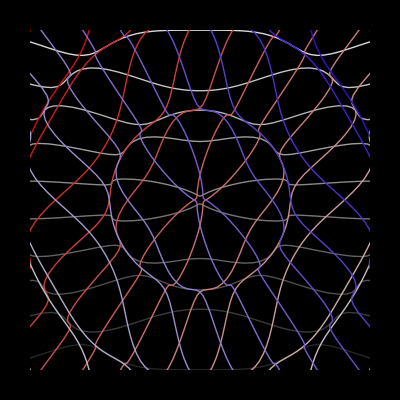
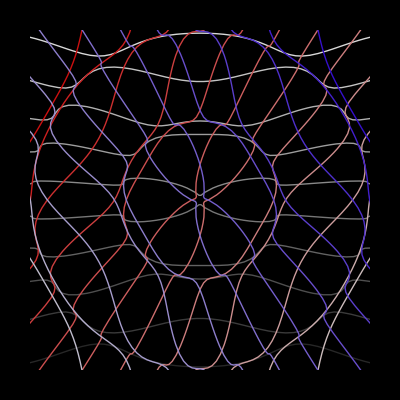
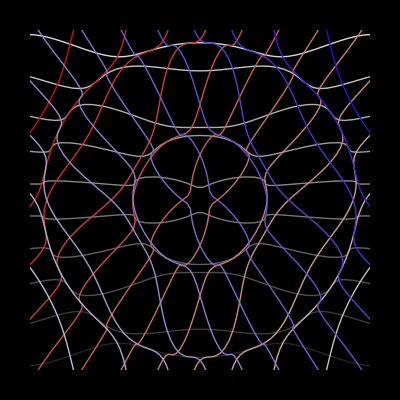
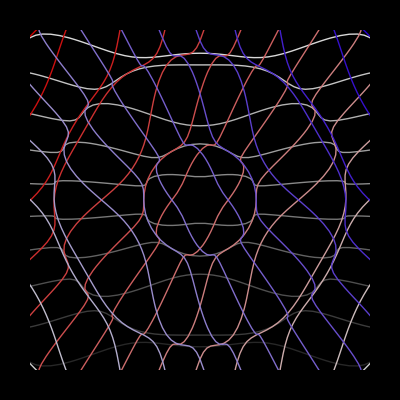
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[gridGP];
gridGP=(IncreaseGraphicsResolution[#1,π/6]&)[N[TriangularGrid[5 π,14]]];
Table[Transform2DGraphicsPlot[gridGP,Function[{x,y},Sin[Norm[{x,y}]+i] Normalize[{x,y}]+{x,y}],Background->GrayLevel[0],Axes->False,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}} (3 π+2)],{i,0,2 π,(2 π)/8}]
```

#### fish net

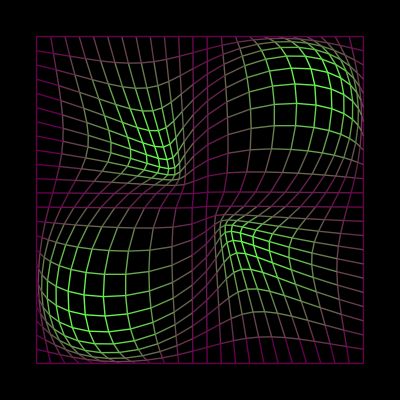

```mathematica
Transform2DPlot[(Sin[x]*Sin[y])*Normalize[{x, y}] + {x, y}, {x, -Pi, Pi}, 
  {y, -Pi, Pi}, PlotPoints -> 24*{1, 1}, ColorFunction -> 
   (RGBColor[0.4, #1, 0.3] & ), Background -> GrayLevel[0], Axes -> False]
```

same function on a polar grid

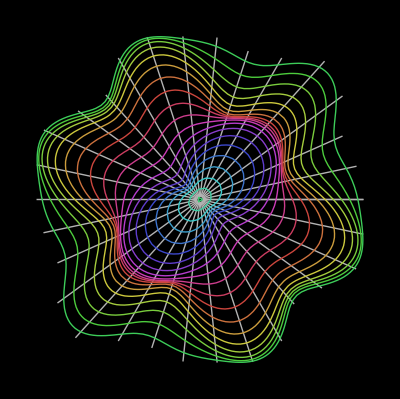

```mathematica
Transform2DGraphicsPlot[PolarGrid[{0.1, 2*Pi, (2*Pi)/20}, 
   {0, 2*Pi, (2*Pi)/30}, {Hue[#1 - 0.6, 0.7, 0.8] & , GrayLevel[0.7] & }], 
  Function[{x, y}, (Sin[x]*Sin[y])*Normalize[{x, y}] + {x, y}], 
  ResolutionLength -> 0.25, AspectRatio -> Automatic, 
  Background -> GrayLevel[0], Axes -> False]
```

same function on a triangular grid

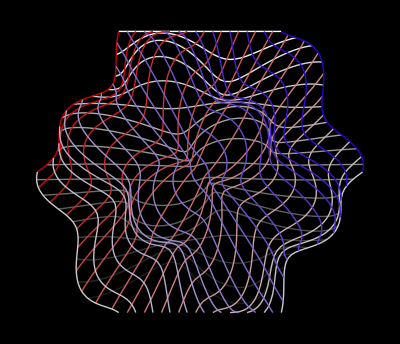

```mathematica
Transform2DGraphicsPlot[TriangularGrid[2 π,20],Function[{x, y}, (Sin[x]*Sin[y])*Normalize[{x, y}] + {x, y}],ResolutionLength->.25,AspectRatio->Automatic,Background->GrayLevel[0],Axes->False]
```

#### burning hole

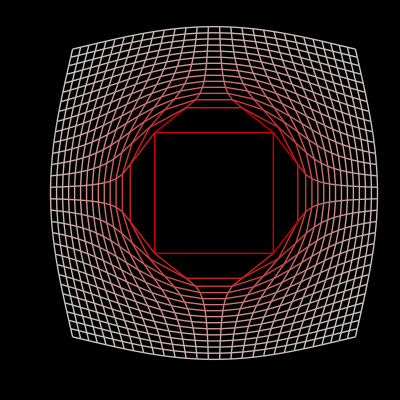

```mathematica
Transform2DPlot[(1/(Norm[{#1,#2}]+2)+4) Normalize[{#1,#2}]+{#1,#2}&,{-1,1} 5,{-1,1} 5,PlotPoints->{1,1} 30,Axes->True,Background->GrayLevel[0]]
```

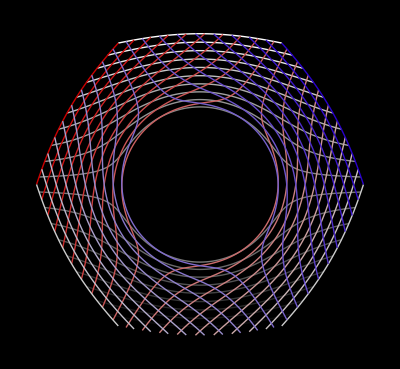

```mathematica
Transform2DGraphicsPlot[TriangularGrid[5,20],(1/(Norm[{#1,#2}]+2)+4) Normalize[{#1,#2}]+{#1,#2}&,ResolutionLength->.2,Background->GrayLevel[0],AspectRatio->Automatic]
```

#### Magnifying glass

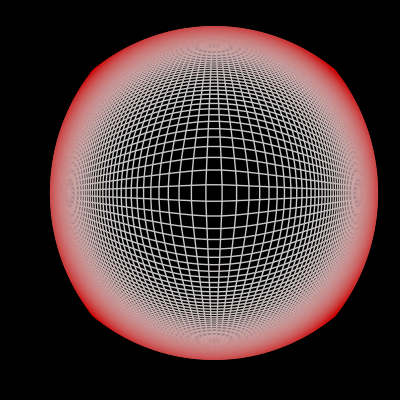

```mathematica
Transform2DPlot[{#1,#2}/(Norm[{#1,#2}]+1/2)&,{-1,1} 3,{-1,1} 3,PlotPoints->{1,1} 134,Background->GrayLevel[0]]
```

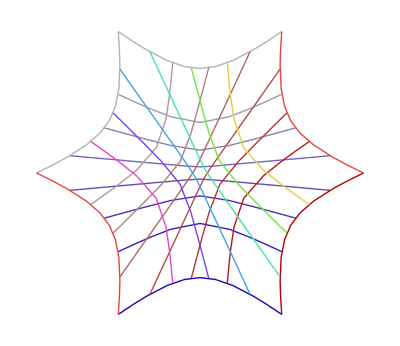

```mathematica
Transform2DGraphicsPlot[TriangularGrid[π,8,{Hue[0.7,#1,0.7]&,Hue[0,#1,0.7]&,Hue[#1,0.7,0.9]&}],{#1,#2}/(Norm[{#1,#2}]-5.01)&,ResolutionLength->0.5,AspectRatio->Automatic]
```

#### a breast

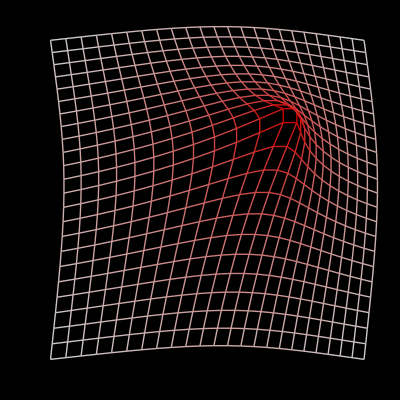

```mathematica
Transform2DPlot[1/(Norm[{x,y}]+1)+{x,y},{x,-1,1},{y,-1,1},PlotPoints->{1,1} 24,Axes->True,Background->GrayLevel[0]]
```

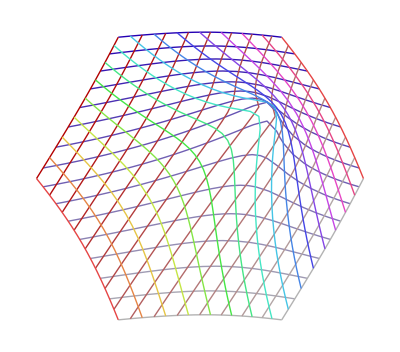

```mathematica
Transform2DGraphicsPlot[TriangularGrid[1,16,{Hue[0.7,#1,0.7]&,Hue[0,#1,0.7]&,Hue[#1,0.7,0.9]&}],Function[{x,y},1/(Norm[{x,y}]+1)+{x,y}],ResolutionLength->0.1,AspectRatio->Automatic]
```

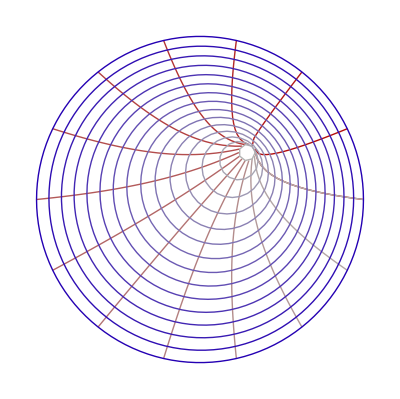

```mathematica
Transform2DGraphicsPlot[PolarGrid[{0.1,2},{0,2 3.14156},{Hue[0.7,#1,0.7]&,Hue[0,1-#1,0.7]&}],Function[{x,y},1/(Norm[{x,y}]+1)+{x,y}],ResolutionLength->0.1,AspectRatio->Automatic]
```

#### {Tan[x], Tan[y]}

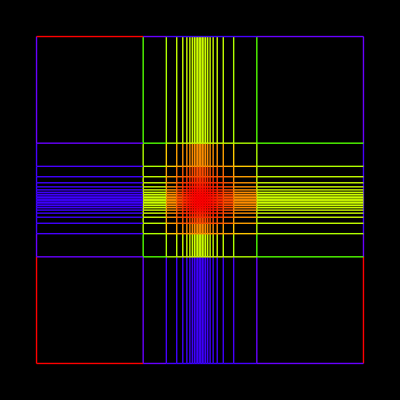

```mathematica
Transform2DPlot[Tan[{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},PlotPoints->{1,1} 24,ColorFunction->Hue,Axes->False,Background->GrayLevel[0]]
```

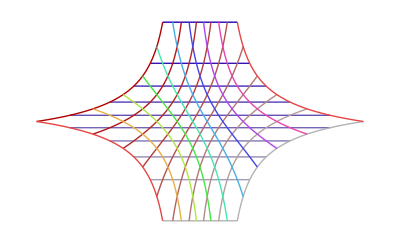

```mathematica
Transform2DGraphicsPlot[TriangularGrid[1.1,10,{Hue[.7,#1,.7]&,Hue[0,#1,.7]&,Hue[#1,.7,.9]&}],Function[{x,y},Tan[{x,y}]],ResolutionLength->.1,AspectRatio->Automatic]
```

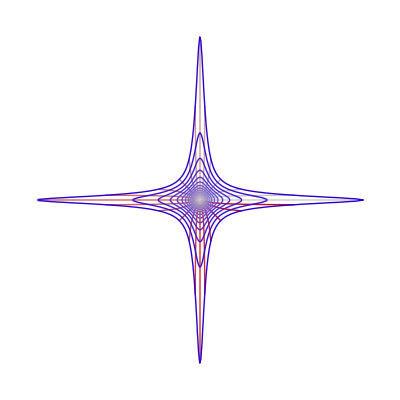

```mathematica
Transform2DGraphicsPlot[PolarGrid[{0.1,1.5},{0,2 3.14159,(2 π)/24}],Function[{x,y},Tan[{x,y}]],ResolutionLength->0.1,AspectRatio->Automatic]
```

#### {y,Sin[y x]}

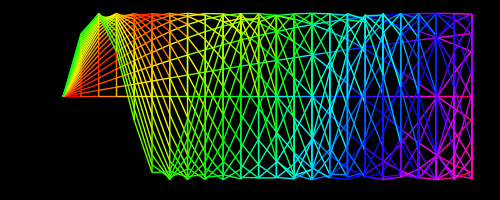

```mathematica
Transform2DPlot[{y,Sin[y x]},{x,0,π},{y,0,2 π},PlotPoints->{1,1} 24,ColorFunction->Hue,Axes->True,Background->GrayLevel[0],Ticks->{Range[0],Range[-5,5,1]}]
```

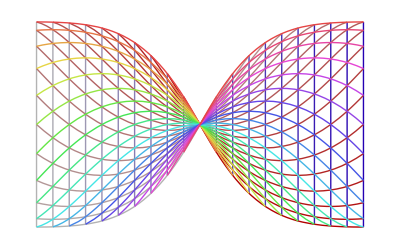

```mathematica
Transform2DGraphicsPlot[TriangularGrid[π/2,21,{Hue[.7,#1,.7]&,Hue[0,#1,.7]&,Hue[#1,.7,.9]&}],Function[{x,y},{y,Sin[y x]}],ResolutionLength->.1,AspectRatio->Automatic]
```

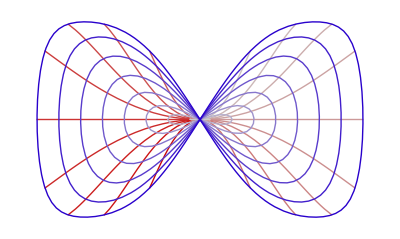
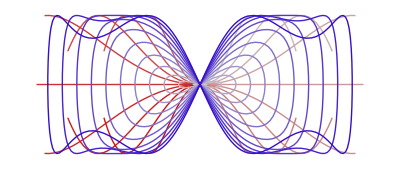
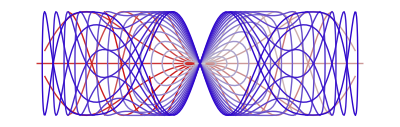

```mathematica
Table[Transform2DGraphicsPlot[PolarGrid[{0.1,i,π/15},{0,2. π,(2 π)/20}],Function[{x,y},{y,Sin[y x]}],ResolutionLength->0.1,AspectRatio->Automatic],{i,π/2,π,π/(2 2)}]
```

#### varing concentric rotation

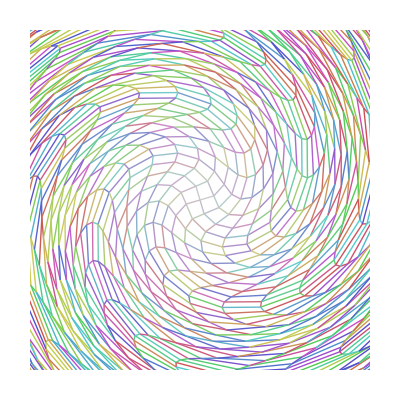

```mathematica
Clear[n];
n=N[π/3];
Transform2DPlot[({{Cos[#1 n],-Sin[#1 n]},{Sin[#1 n],Cos[#1 n]}}&)[Norm[{x,y}]].{x,y},{x,-2 π,2 π},{y,-2 π,2 π},PlotRange->{{-1,1},{-1,1}} 3.1,ColorFunction->(Hue[RandomReal[],√#1,0.8]&),PlotPoints->47,Axes->False]
```

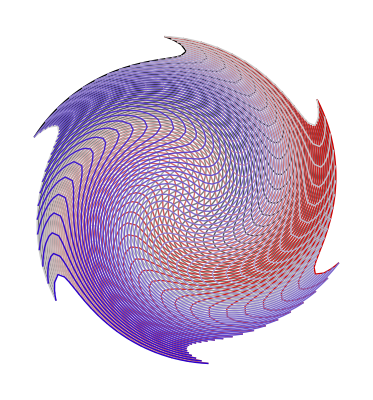

```mathematica
Clear[n];n=N[π/3];
Transform2DGraphicsPlot[TriangularGrid[π,49],Function[{x,y},({{Cos[#1 n],-Sin[#1 n]},{Sin[#1 n],Cos[#1 n]}}&)[Norm[{x,y}]].{x,y}],ResolutionLength->.2,AspectRatio->Automatic]
```

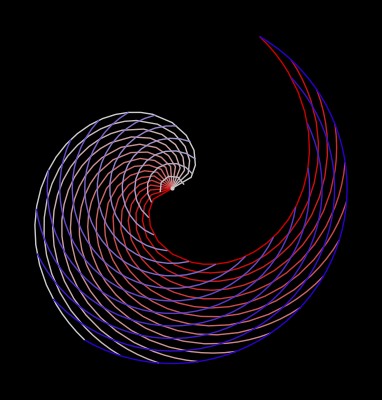

```mathematica
Clear[n];
n=N[π/3];
Transform2DGraphicsPlot[PolarGrid[{0,4},{0,π}],Function[{x,y},({{Cos[#1 n],-Sin[#1 n]},{Sin[#1 n],Cos[#1 n]}}&)[Norm[{x,y}]].{x,y}],ResolutionLength->.5,AspectRatio->Automatic,Background->GrayLevel[0]]
```

#### blackhole

If[N[Norm[{#1,#2}]]<1,(#1^2+#2^2)^2 {#1,#2},{#1,#2}]&

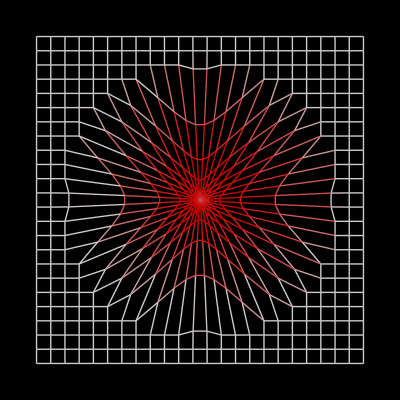

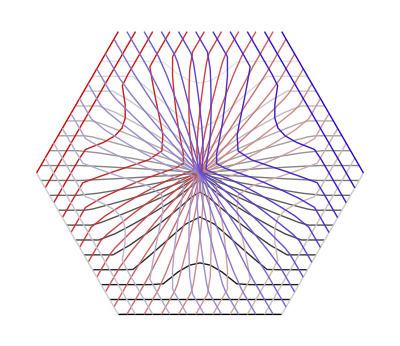

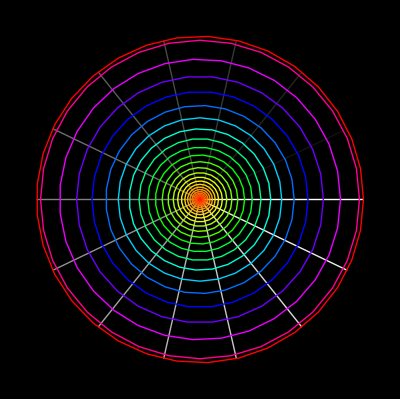

```mathematica
Clear[f]
f=If[N[Norm[{#1,#2}]]<1,(#1^2+#2^2)^2 {#1,#2},{#1,#2}]&
Transform2DPlot[f[x,y],{x,-1.2,1.2},{y,-1.2,1.2},Axes->False,Background->GrayLevel[0]]

Transform2DGraphicsPlot[TriangularGrid[1.2,20],f[#1,#2]&,Axes->False,AspectRatio->Automatic,ResolutionLength->0.2]

Transform2DGraphicsPlot[PolarGrid[{0,1.025,.025},{0,2 π},{Hue[#1^4]&,GrayLevel}],Function[{x,y},f[x,y]],ResolutionLength->0.2,AspectRatio->Automatic,PlotRange->All,Background->GrayLevel[0]]
```

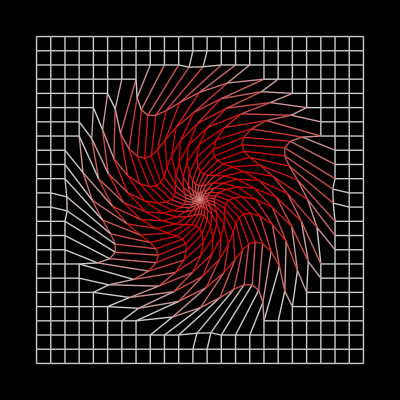

```mathematica
Clear[f,n]
n=N[2];
f=Function[{x,y},If[N[Norm[{x,y}]]<1,(RotationMatrix[(1-#1) n]&)[x^2+y^2].{x,y} (x^2+y^2),{x,y}]];
Transform2DPlot[f[x,y],{x,-1.2,1.2},{y,-1.2,1.2},Axes->False,Background->GrayLevel[0],PlotPoints->{24,24}]
```

## Graphics Gallery 2

#### Inversion of triangular grid.

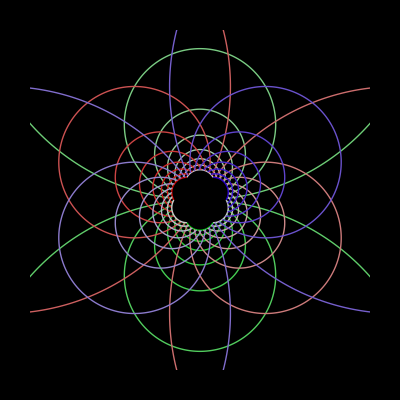

```mathematica
Transform2DGraphicsPlot[Show[Graphics[TriangularGrid[1.2,16,{Hue[.35,1-#1,.8]&,Hue[0,#1,.8]&,Hue[.7,#1,.8]&}]],AspectRatio->Automatic],1/Conjugate[#1]&,Axes->False,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}} 4.5,Background->GrayLevel[0]]
```

#### definition of geometric inversion

```mathematica
Clear[inversion];
inversion::"usage"=" inversion[{c1,c2}, r] returns a pure function f:R^2->R^2, where f is the inversion transformation with center {c1,c2} and radius r. inversion[] is a shorthand for inversion[{0,0}, 1]. Usage Example: inversion[{1,1}, 2][x,y]";
inversion[{c1_,c2_},r_]:=If[N[{c1,c2}]==N[{#1,#2}],{∞,∞},(({#1,#2}-{c1,c2}) r^2)/(Plus@@(({#1,#2}-{c1,c2})^2))+{c1,c2}]&;
inversion[][0,0]:={∞,∞}
inversion[]:={#1,#2}/(Plus@@({#1,#2}^2))&
```

Following is alternative, faster version definition thru Mathematica's complex number engine.

```mathematica
Clear[inversion]
inversion::"usage"=" inversion[{c1,c2}, r] returns a pure function f:R^2->R^2, where f is the geometric inversion transformation with center {c1,c2} and radius r. inversion[] is a shorthand for inversion[{0,0}, 1]. Usage Example: inversion[{1,1}, 2][x,y]";
inversion[]=inversion[{0,0},1];
inversion[{0,0},1]=({Re[#1],Im[#1]}&)[Conjugate[1/(#1+#2 ⅈ)]]&;
inversion[{0,0},r_]=({Re[#1],Im[#1]}&)[Conjugate[r^2/(#1+#2 ⅈ)]]&;
inversion[{c1_,c2_},r_]=({Re[#1],Im[#1]}&)[Conjugate[r^2/((#1+#2 ⅈ)-(c1+c2 ⅈ))]+(c1+c2 ⅈ)]&;
```

#### Repeated inversion of circles.

The pre-image is n non-overlapping circles evenly distributed around the origin, plus a circle centered around the origin but not touching the others.

```mathematica
Clear[n, nestLevel, resolution, li, gra];

n = 5; (* n is the number of circles. Try 2, 3, 4, 5, 6*)
nestLevel = 2; (* greater than 2 may take a long time *)
resolution = .08; (* smaller == smoother == longer *) 

(* this generate n circles distributed around a center *)
li = N@ Rest@ Table[ Circle[{Sin@t, Cos@t}, .98 Sin[(2 Pi/n)/2]],
	{t, 0, 2 Pi, 2 Pi/n}];

(* this adds a center circle *)
li = N@ Join[li, {Circle[{0,0}, 1- Sin[(2 Pi/n)/2] ]}];

(* adds color *)
gra = N@ Transpose[{
	Rest@ Table[Hue[i], {i,0,1,1/(Length@li)}],
	li
}]
```

{{Hue[0.16666666666666666],Circle[{0.951057,0.309017},0.57603]},{Hue[0.3333333333333333],Circle[{0.587785,-0.809017},0.57603]},{Hue[0.5],Circle[{-0.587785,-0.809017},0.57603]},{Hue[0.6666666666666666],Circle[{-0.951057,0.309017},0.57603]},{Hue[0.8333333333333334],Circle[{0.,1.},0.57603]},{Hue[1.],Circle[{0.,0.},0.412215]}}

(* may take a minute or more. *)

```mathematica
result=Nest[Outer[g[First[Transform2DGraphicsPlot[#1,#2,ResolutionLength->resolution,DisplayFunction->Identity]]]&,g[#1],g@@(li/.Circle->inversion)]&,g[gra],nestLevel]
```

Note: an intermediate head g must be used because otherwise
Outer will pick any small element in the Graphics. With a temporary
head g, Outer will only pair elements with head g only.
Also, the temporary head cannot be Graphics, because, arguments other
then the first in Graphics will automatically be deleted, presumably
because Graphics is defined to take only one argument, with the rest
being options.

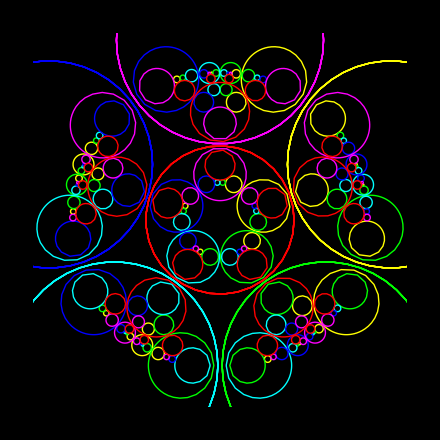

```mathematica
Show[Graphics[result/.g->List],AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}},Background->GrayLevel[0]]
```

## gallery 3

#### a linear map with eigen vectors

This is a linear mapping by the matrix (3 | -2
1 | 0). The blue lines are its eigen vectors.

```mathematica
Clear[matrix,gridGP];
matrix={{3,-2},{1,0}};
gridGP=PolarGrid[{1,2,.1},{0,6,.1},{GrayLevel[1-#1]&,Hue}];
```

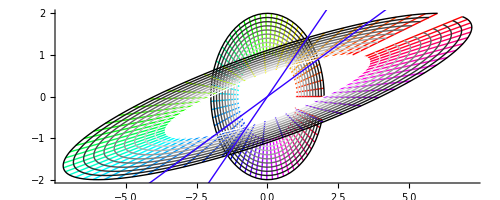

```mathematica
Transform2DGraphicsPlot[gridGP,matrix.{#1,#2}&,Prolog->gridGP,Epilog->{Hue[.7],Line/@Transpose[(6 {-#1,#1}&)[Eigenvectors[matrix]]]},Axes->True,AspectRatio->Automatic]
```